# Nakagami channel detection probability (large m n comparison)

This notebook tests the accuracy of the large m n approximate method against Annamalai’s exact method for cooperative networks of energy detectors operating on Nakagami-faded channels.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

27/06/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
Unprotect["Global`*"];
ClearAll["Global`*"];
```

```mathematica
path=NotebookDirectory[];
SetDirectory[path];
<<definitions.m
<<plots.m
```

## Variables

Here, we define the ranges of values to be used for each parameter.

```mathematica
nRange={1,2,3,4,5,10,20};
mRange={0.5,1,1.5,2};
samplesRange={1000,10000,50000};
snrdbRange=Range[0,-21,-1];
snrRange=10^(snrdbRange/10);
pfRange={49/100,30/100,20/100,10/100,5/100,1/100,5/1000,1/1000,5/10000,1/10000,5/100000,1/100000};
```

Here, we select n and m so that m n ∈ I and m n ≥ 10 (i.e. large m n only):

```mathematica
{nRange,mRange,mnRange}=Select[Flatten[Table[{nRange⟦i⟧,mRange⟦j⟧,nRange⟦i⟧ mRange⟦j⟧},{i,Length[nRange]},{j,Length[mRange]}],1],Ceiling[##[[3]]]==##[[3]]&&##[[3]]≥10&]//Transpose;
```

## Calculations

Calculate the probability of detection, for each set of parameter values defined previously, using the exact and approximate methods:

```mathematica
exact=Table[ProbabilityOfDetection[M,snr,λ[M,pf,nRange[[mn]],Method->"Exact"],nRange[[mn]],ChannelType->{"Nakagami",mRange[[mn]]},Method->"ExactAnnamalai",DatabaseLookup->True],{snr,snrRange},{mn,Length[mnRange]},{M,samplesRange},{pf,pfRange}];
```

```mathematica
approx=Table[ProbabilityOfDetection[M,snr,λ[M,pf,nRange[[mn]]],nRange[[mn]],ChannelType->{"Nakagami",mRange[[mn]]},Method->"ApproximateLargeMN"]//N,{snr,snrRange},{mn,Length[mnRange]},{M,samplesRange},{pf,pfRange}];
```

Calculate various error metrics:

```mathematica
error=exact-approx;
absError=Abs[error];
relError=error/exact;
absRelError=Abs[relError];
```

## Results

### Detection probabilities

Plots of detection probabilities against signal to noise ratio, for the defined parameter sets, using the exact and approximate methods:

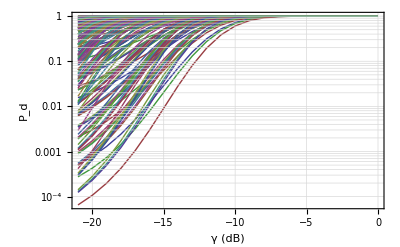
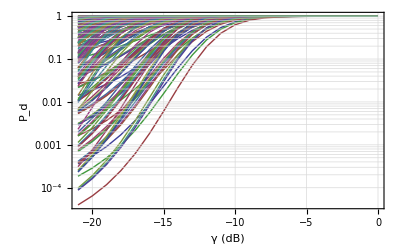

```mathematica
Table[CustomPlot[snrdbRange,y,{"γ (dB)","P_d"}],{y,{exact,approx}}]
```

### Error statistics

#### Error and absolute error

Probability density function of the approximation error:

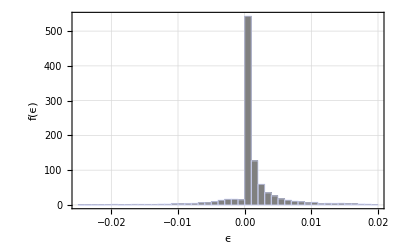

```mathematica
CustomHistogram[error,{"ϵ","f(ϵ)"}]
```

Histogram statistics:

```mathematica
StatsTable[error]
```

| μ | σ
 | 0.000946299 | 0.00419554

Largest errors:

```mathematica
MaxErrorsTable[absError,10]
```

γ (dB) | n | m | M | pf | ϵ | ϵ_r
-10. | 5. | 2. | 1000. | 0.00001 | -0.0247001 | -0.0408292
-12. | 10. | 1. | 1000. | 0.00001 | -0.0237917 | -0.0473223
-17. | 10. | 1. | 10000. | 0.00001 | -0.022434 | -0.0434023
-19. | 5. | 2. | 50000. | 0.00001 | -0.0221581 | -0.0428621
-11. | 5. | 2. | 1000. | 0.0001 | -0.0221099 | -0.0425857
-12. | 10. | 1. | 1000. | 0.00005 | -0.0219585 | -0.0370586
-11. | 5. | 2. | 1000. | 0.00005 | -0.0215651 | -0.0453929
-13. | 20. | 0.5 | 1000. | 0.00001 | -0.021465 | -0.0345152
-14. | 20. | 0.5 | 1000. | 0.00005 | -0.0208257 | -0.0425111
-14. | 20. | 0.5 | 1000. | 0.0001 | -0.0204722 | -0.0383629

#### Relative error and absolute relative error

Probability density function of the relative approximation error:

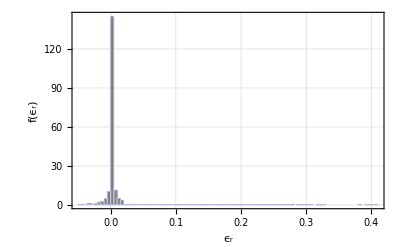

```mathematica
CustomHistogram[relError,{"ϵ_r","f(ϵ_r)"}]
```

Histogram statistics:

```mathematica
StatsTable[relError]
```

| μ | σ
 | 0.00765431 | 0.0370411

Largest relative errors:

```mathematica
MaxErrorsTable[absRelError,10]
```

γ (dB) | n | m | M | pf | ϵ | ϵ_r
-18. | 5. | 2. | 1000. | 0.00001 | 0.00017255 | 0.408562
-19. | 5. | 2. | 1000. | 0.00001 | 0.000080258 | 0.404864
-17. | 5. | 2. | 1000. | 0.00001 | 0.00042287 | 0.404714
-20. | 5. | 2. | 1000. | 0.00001 | 0.0000427642 | 0.39906
-21. | 5. | 2. | 1000. | 0.00001 | 0.0000257536 | 0.393366
-16. | 5. | 2. | 1000. | 0.00001 | 0.00113267 | 0.382958
-19. | 5. | 2. | 1000. | 0.00005 | 0.000242645 | 0.329125
-15. | 5. | 2. | 1000. | 0.00001 | 0.00300215 | 0.328983
-20. | 5. | 2. | 1000. | 0.00005 | 0.000139936 | 0.327661
-19. | 10. | 1. | 1000. | 0.00001 | 0.000212051 | 0.327327